## Plot of Single EWS for X Variable

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_models/cr_model"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,20,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
windowComps=100;
dt2=0.5;
al=25;
ah=42;
tmax=200;
psdTime=150;
```

## Import Data

```mathematica
ewsSingles=Import["data_export/cr_ews_1/ews_singles.csv"];
specData=Import["data_export/cr_ews_1/pspecs.csv"];
```

## Trajectory Plots

```mathematica
(* columns *)
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-4 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax}

```mathematica
ewsSingles[[-1,3]]
```

199.5

```mathematica
(* realisation nuber *)
relNum=2;
xSeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"x",_,_}][[;;,{3,4}]];
ySeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"y",_,_}][[;;,{3,4}]];
```

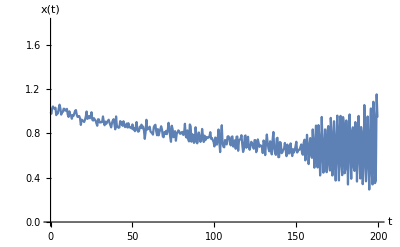

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[xSeries,
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","x(t)"},
PlotRange->{0,1.8},
ImagePadding->padTop]
```

## Bifurcation diagram X

### Specifications

```mathematica
(* Import data *)
rawdata=Import["bifurcation_data/cr1x.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[eqColors,{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of a *)
abifVals=fulldata[[;;,1]]*10;
tbifVals=(abifVals-al)*tmax /(ah-al);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections=Append[nodeSections,Cases[nodeSections[[7]],{_,x_,_,_}/;x<=0.75]];
nodeSections[[7]]=Cases[nodeSections[[7]],{_,x_,_,_}/; x>=0.65] ;(* had to seperate out brances for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}];
```

```mathematica
(* Take relevant branches of node sections *)
delList={1,2,3,6};
branchesNums=Complement[Range[1,numBranches],delList]
```

{4,5,7,8}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

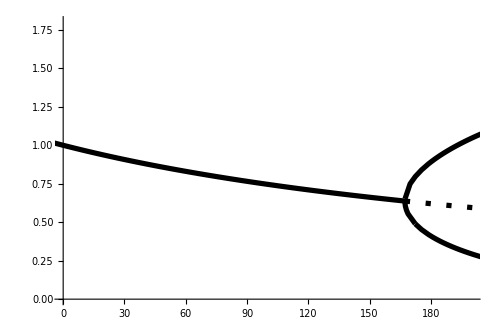

```mathematica
(* Make plot *)
bifPlotNormal=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,1.8}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

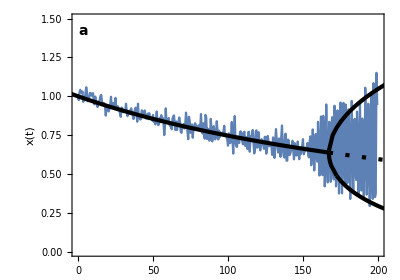

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.2;
trajVal=0.7;

bifTrajX=Show[{plotX,bifPlotNormal},
PlotRange->{{0,tmax},{0,1.5}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x(t)",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
AspectRatio->0.7,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]]}]
```

## Single EWS Plots

### Variance

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,8}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,5}];
```

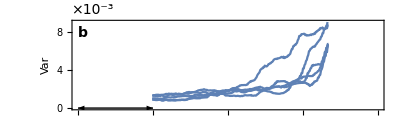

```mathematica
plotVar=ListLinePlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.009}},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{Transpose[{Range[0,10,2]*10^(-3),Range[0,10,2]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-3",14],indexPos],
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}]
```

### Lag-1 Autocorrelation

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,9}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,5}];
```

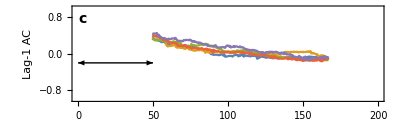

```mathematica
plotLag1AC=ListLinePlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"Lag-1 AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{-1,1}},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,-0.2 (* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,-0.2 (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Lag-2 Autocorrelation

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,10}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,5}];
```

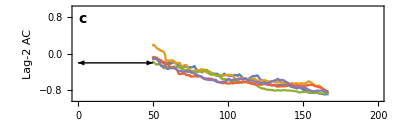

```mathematica
plotLag2AC=ListLinePlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"Lag-2 AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{-1,1}},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,-0.2 (* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,-0.2 (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Lag-4 Autocorrelation

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,11}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,5}];
```

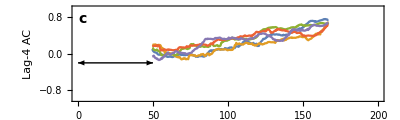

```mathematica
plotLag4AC=ListLinePlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"Lag-4 AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{-1,1}},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,-0.2 (* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,-0.2 (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation combined

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,9,10,11}]],
{_,"x",_,_,_,_}]⟦;;,{3,i}⟧,
{i,{4,5,6}}];
```

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,3,4}]],Table["τ="<>ToString[i],{i,{1,2,4}}],Spacings->{0,0.1}]
```

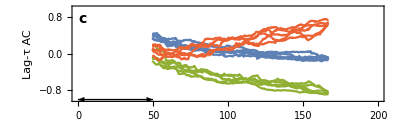

```mathematica
plotLagnAC=ListLinePlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
FrameLabel->{{"Lag-τ AC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},{-1,1}},
PlotStyle->TMBcolours[[{1,3,4}]],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
PlotLegends->Placed[legend,{0.15,0.75}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,-1(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,-1 (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

### Smax

```mathematica
Position[ewsSingles[[1]],"Smax"][[1,1]]
```

22

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,22}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,5}];
```

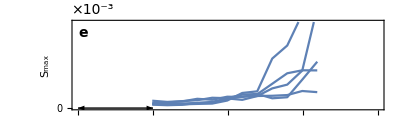

```mathematica
plotSmax=ListPlot[series,
Joined->True,
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.002}},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"S_max",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameTicks->{{Transpose[{10^(-3)*Range[0,10,1],Range[0,10,1]}],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["×10^-3",14],indexPos],
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

### AIC

```mathematica
Position[ewsSingles[[1]],"AIC fold"][[1,1]]
```

15

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[{1,4}]],{"ω_fold","ω_hopf"},Spacings->{0,0.1}]
```

```mathematica
seriesFold=Table[
Cases[
ewsSingles[[2;;,{1,2,3,15}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,5}];
```

```mathematica
seriesHopf=Table[
Cases[
ewsSingles[[2;;,{1,2,3,16}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,5}];
```

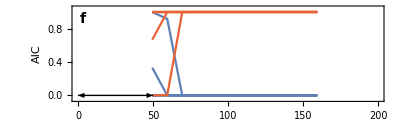

```mathematica
plotAIC=ListLinePlot[Join[seriesFold,seriesHopf],
Joined->True,
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
PlotStyle->TMBcolours[[{1,1,1,1,1,4,4,4,4,4}]],
PlotLegends->Placed[legend,{0.15,0.75}],
Frame->True,
FrameLabel->{{"AIC",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}]
```

### Power Spectrum

```mathematica
specData//Dimensions
```

{4921,5}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[2;;,3]]]
```

{49.5,59.5,69.5,79.5,89.5,99.5,109.5,119.5,129.5,139.5,149.5,159.5}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{"TemperatureMap",timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

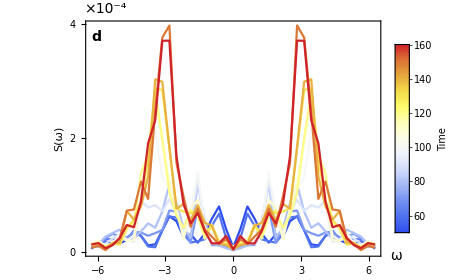

```mathematica
(* normalise to map each trajectory to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
plotPspec=ListLinePlot[pspecs,
PlotRange->All,
PlotStyle->Thread@{ColorData["TemperatureMap"]/@plotTimesUnit},
LabelStyle->13,
Frame->True,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.7,
FrameLabel->{{"S(ω)",None},{None,None}},
PlotRangeClipping->False,
Epilog->{Text[Style["×10^-4",14],Scaled[{0.065,1.05}]],
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]]},
FrameTicks->{{Transpose[{Range[0,10,1]*10^(-4),Range[0,10,1]}],Automatic},{Automatic,Automatic}},
PlotLegends->Placed[colLegend,Scaled[{0.9,0.55}]]]
```

## Grid: Single EWS

```mathematica
Grid[{{bifTrajX,plotPspec},{plotVar,plotSmax},{plotLagnAC,plotAIC},{},{}},Spacings->{0,0}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
 | 
 |

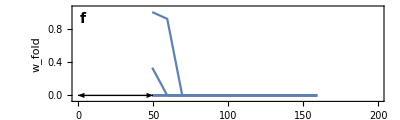
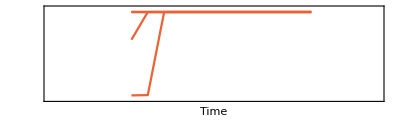
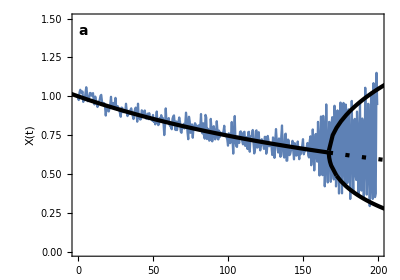
{-Graphics--Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{plotAIC,plotVar,plotLag1AC,plotLag2AC,plotLag4AC,plotLagnAC,plotPspec,bifTrajX}
```

## Ensemble Plot